```mathematica
Stability analysis of RM1 and RM2;
```

Constants:

```mathematica
alpha = p = 2;
beta = q =1;
c= 1;
g = 1;
d =2;
f = 2;
```

normalized values to 6022 (meeting the condition z0^(1/q) > x0*a0^f)

```mathematica
x0= 1;
y0= 1.5;
z0= 3.5;
a0= 1.125;
b0 = 1.5;
```

## Cases from Table 4

### RM2s Case 1 : x' = y' = 0, var a, b Case 2 : y' = a' = 0, var x, b Case 3 : a' = b' = 0, var x, y

Steady States Case 1

```mathematica
RM2sc1 = Solve[{-x*a^f - y*b*a^g== 0, x*a^f - y*b*a^g== 0}, {a, b}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→0},{a→0,b→0}}

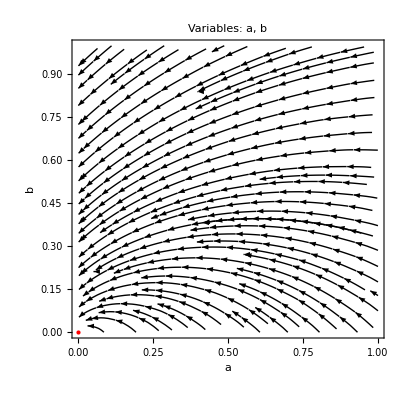

```mathematica
Show[StreamPlot[{-x0 *a^f - y0*b*a^g,x0 *a^f - y0*b*a^g},{a, 0, 1}, {b,0,1},Frame->True, FrameStyle->Directive[Black,15],FrameLabel->{Style["a", 18], Style["b", 18]},FrameTicks->Automatic, FrameTicksStyle->Directive[Thick, Black, 15],LabelStyle->Directive[Black], PlotLabel->Style["Variables: a, b", Large], StreamColorFunction->None,StreamStyle->Black], Graphics[{PointSize[Large],Red,Point[{0,0}]}], FrameStyle-> {Thick, Directive[Thick, Black]}]
```

Type of critical point

Calculate the Jacobian

```mathematica
Jc1=D[{-x*a^f - y*b*a^g,x*a^f - y*b*a^g},{{a,b}}]
```

{{-2 a x-b y,-a y},{2 a x-b y,-a y}}

Calculate the Jacobian for the found steady states

```mathematica
Jsc1 = Jc1/. RM2sc1[[2]]
```

{{0,0},{0,0}}

Steady States Case 2

```mathematica
RM2sc2 = Solve[{z^(1/p)-x*a^f== 0,x*a^f - y*b*a^g== 0}, {x, b}]
```

{{x→(√z)/a^2,b→(√z)/(a y)}}

Steady State at given values

```mathematica
solRM2sc2=RM2sc2[[1]]/. {y->y0, z->z0, a->a0};
xsolc2 = (Part[solRM2sc2, 1]/. Rule->List)[[2]];
bsolc2 = (Part[solRM2sc2, 2]/. Rule->List)[[2]];
```

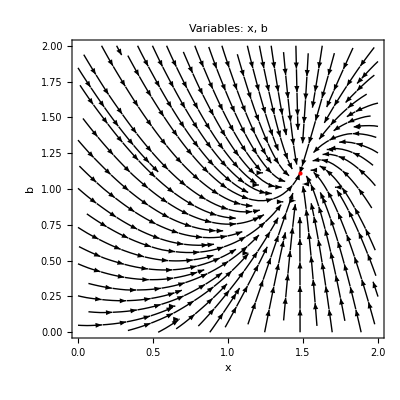

```mathematica
Show[StreamPlot[{z0^(1/p)-x*a0^f,x*a0^f - y0*b*a0^g},{x, 0, 2}, {b,0,2}, Frame-> True,FrameStyle->Directive[Black,18],FrameLabel->{Style["x", 18], Style["b", 18]},FrameTicks->Automatic, FrameTicksStyle->Directive[Thick, Black, 15],LabelStyle->Directive[Black], PlotLabel->Style["Variables: x, b", Large], StreamColorFunction->None,StreamStyle->Black], Graphics[{PointSize[Large],Red,Point[{xsolc2,bsolc2}]}], FrameStyle-> {Thick, Directive[Thick, Black]}]
```

Type of critical point

Calculate the Jacobian

```mathematica
Jc2=D[{z^(1/p)-x*a^f,a^f - y*b*a^g},{{x,b}}]
```

{{-a^2,0},{0,-a y}}

Calculate the Jacobian for the found steady states

```mathematica
Jc21 = Jc2/. RM2sc2 [[1]]
```

{{-a^2,0},{0,-a y}}

Eigen value equation (expansion of the characteristic equation)

```mathematica
eve1 = Solve[l^2 - l*Tr[Jc21] + Det[Jc21] ==0, l]
```

{{l→-a^2},{l→-a y}}

Analyse the sign of Tr[J], Det[J] and Tr[J]^2 - 4 Det[J]

```mathematica
Trc2 = Tr[Jc21]
Dc2  = Det[Jc21]
Sc2 = Tr[Jc21]^2-4Det[Jc21]
Simplify[Sc2]
```

-a^2-a y

a^3 y

-4 a^3 y+(-a^2-a y)^2

a^2 (a-y)^2

Steady States Case 3

```mathematica
RM2sc3 = Solve[{z^(1/p)-x*a^f== 0,z^(1/q)-y*b*a^g== 0}, {x, y}]
```

{{x→(√z)/a^2,y→z/(a b)}}

Steady State at given values

```mathematica
solRM2sc3=RM2sc3[[1]]/. { z->z0, a->a0, b->b0};
xsolc3 = (Part[solRM2sc3, 1]/. Rule->List)[[2]];
ysolc3 = (Part[solRM2sc3, 2]/. Rule->List)[[2]];
```

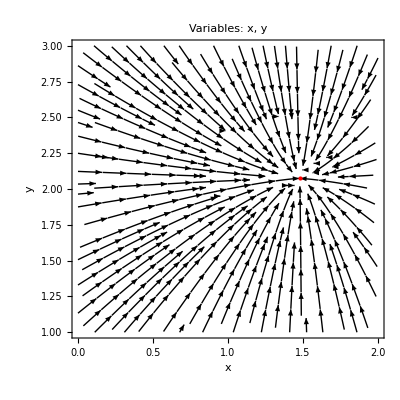

```mathematica
Show[StreamPlot[{z0^(1/p)-x*a0^f,z0^(1/q) - y*b0*a0^g},{x, 0, 2}, {y,1,3}, Frame-> True,FrameStyle->Directive[Black,18],FrameLabel->{Style["x", 18], Style["y", 18]},FrameTicks->Automatic, FrameTicksStyle->Directive[Thick, Black, 15],LabelStyle->Directive[Black], PlotLabel->Style["Variables: x, y", Large], StreamColorFunction->None,StreamStyle->Black], Graphics[{PointSize[Large],Red,Point[{xsolc3,ysolc3}]}], FrameStyle-> {Thick, Directive[Thick, Black]}]
```

Type of critical point

Calculate the Jacobian

```mathematica
Jc3=D[{z^(1/p)-x*a^f,z^(1/q)-y*b*a^g},{{x,y}}]
```

{{-a^2,0},{0,-a b}}

Calculate the Jacobian for the found steady states

```mathematica
Jc31 = Jc3/. RM2sc3 [[1]]
```

{{-a^2,0},{0,-a b}}

Eigen value equation (expansion of the characteristic equation)

```mathematica
eve3 = Solve[l^2 - l*Tr[Jc31] + Det[Jc31] ==0, l]
```

{{l→-a^2},{l→-a b}}

Analyse the sign of Tr[J], Det[J] and Tr[J]^2 - 4 Det[J]

```mathematica
Trc3 = Tr[Jc31]
Dc3  = Det[Jc31]
Sc3 = Tr[Jc31]^2-4Det[Jc31]
Simplify[Sc3]
```

-a^2-a b

a^3 b

-4 a^3 b+(-a^2-a b)^2

a^2 (a-b)^2

### RM2 Case 4 : x' = y' = 0, var a, b => same as case 1 RM2s Case 5 : x' = a' = 0, var y, b Case 6 : y' = a' = 0, var x, b => same as case 2 RM2s Case 7: a' = b' = 0, var x, y Case 8: a' = 0, var x, y, b

Steady States Case 5

```mathematica
RM2c5 = Solve[{z^(1/q)-y*b*a^g-y*a^d== 0, x*a^f - y*b*a^g== 0}, {y, b}]
```

{{y→(-a^2 x+z)/a^2,b→-(a^3 x)/(a^2 x-z)}}

Steady State at given values

```mathematica
solRM2c5=RM2c5[[1]]/. {x->x0, z->z0, a->a0};
ysolc5 = (Part[solRM2c5, 1]/. Rule->List)[[2]];
bsolc5 = (Part[solRM2c5, 2]/. Rule->List)[[2]];
```

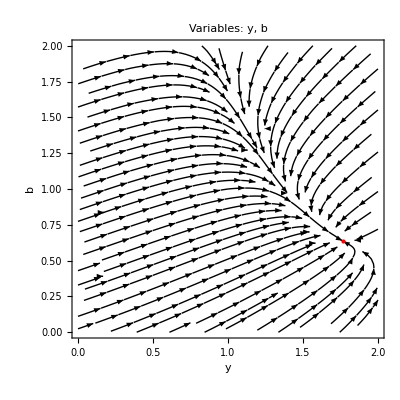

```mathematica
Show[StreamPlot[{z0^(1/q)-y*b*a0^g-y*a0^d,x0*a0^f - y*b*a0^g},{y, 0, 2}, {b,0,2}, Frame->True, FrameStyle->Directive[Black,15],FrameLabel->{Style["y", 18], Style["b", 18]},FrameTicks->Automatic, FrameTicksStyle->Directive[Thick,Black, 15],LabelStyle->Directive[Black], PlotLabel->Style["Variables: y, b", Large], StreamColorFunction->None,StreamStyle->Black], Graphics[{PointSize[Large],Red,Point[{ysolc5 ,bsolc5 }]}], FrameStyle-> {Thick, Directive[Thick, Black]}]
```

Steady States Case 7

```mathematica
RM2c7 = Solve[{z^(1/p)-x*a^f== 0,z^(1/q)-y*b*a^g - y*a^d== 0}, {x, y}]
```

{{x→(√z)/a^2,y→z/(a (a+b))}}

1.1 Steady State at given values

```mathematica
solRM2c7=RM2c7[[1]]/. { z->z0, a->a0, b->b0};
xsolc7 = (Part[solRM2c7, 1]/. Rule->List)[[2]];
ysolc7= (Part[solRM2c7, 2]/. Rule->List)[[2]];
```

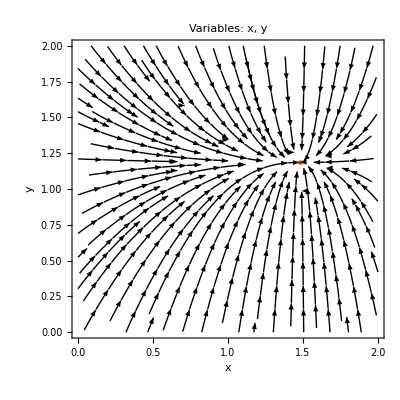

```mathematica
Show[StreamPlot[{z0^(1/p)-x*a0^f,z0^(1/q)-y*b0*a0^g - y*a0^d},{x, 0, 2}, {y,0,2}, Frame->True, FrameStyle->Directive[Black,15],FrameLabel->{Style["x", 18], Style["y", 18]},FrameTicks->Automatic, FrameTicksStyle->Directive[Thick,Black, 15],LabelStyle->Directive[Black], PlotLabel->Style["Variables: x, y", Large], StreamColorFunction->None,StreamStyle->Black], Graphics[{PointSize[Large],Red,Point[{xsolc7 ,ysolc7 }]}], FrameStyle-> {Thick, Directive[Thick, Black]}]
```

Type of critical point

Calculate the Jacobian

```mathematica
Jc7=D[{z^(1/p)-x*a^f,z^(1/q)-y*b*a^g - y*a^d},{{x,y}}]
```

{{-a^2,0},{0,-a^2-a b}}

Calculate the Jacobian for the found steady states

```mathematica
Jc71 = Jc7/. RM2c7 [[1]]
```

{{-a^2,0},{0,-a^2-a b}}

Eigen value equation (expansion of the characteristic equation)

```mathematica
eve7 = Solve[l^2 - l*Tr[Jc71] + Det[Jc71] ==0, l]
```

{{l→-a^2},{l→-a^2-a b}}

Analyse the sign of Tr[J], Det[J] and Tr[J]^2 - 4 Det[J]

```mathematica
Trc7 = Tr[Jc71]
Dc7  = Det[Jc71]
Sc7 = Tr[Jc71]^2-4Det[Jc71]
Simplify[Sc7]
```

-2 a^2-a b

a^4+a^3 b

(-2 a^2-a b)^2-4 (a^4+a^3 b)

a^2 b^2

Steady States Case 8

```mathematica
RM2c8 = Solve[{z^(1/p)-x*a^f== 0, z^(1/q)-y*b*a^g-y*a^d== 0, x*a^f - y*b*a^g== 0}, {x, y,b}]
```

{{x→(√z)/a^2,y→(-√z+z)/a^2,b→(a+a √z)/(-1+z)}}

Steady State at given values

```mathematica
solRM2c8=RM2c8[[1]]/. { z->z0, a->a0};
xsolc8 =(Part[solRM2c8, 1]/. Rule->List)[[2]];
ysolc8 =(Part[solRM2c8, 2]/. Rule->List)[[2]];
bsolc8 =(Part[solRM2c8, 3]/. Rule->List)[[2]];
```

```mathematica
Show[StreamPlot3D[{z0^(1/p)-x*a0^f, z0^(1/q)-y*b*a0^g-y*a0^d, x*a0^f - y*b*a0^g},{x, -40, 40}, {y,-40,40},{b, -40, 40}, StreamMarkers->"Arrow", StreamColorFunction->(Blend[{Green,Blue,Black},#5]&), StreamPoints->60, StreamStyle->Thickness[2], AxesLabel-> {"x", "y", "b"}],  Graphics3D[{PointSize[Large],Red,Point[{xsolc8,ysolc8, bsolc8}]}]]
```

-Graphics3D-

```mathematica
Show[SliceVectorPlot3D[{z0^(1/p)-x*a0^f, z0^(1/q)-y*b*a0^g-y*a0^d, x*a0^f - y*b*a0^g},{ x== xsolc8, y==ysolc8,b==bsolc8},{x, -10, 10}, {y,-10,10},{b, -10, 10}, PlotTheme->"Scientific", VectorAspectRatio->0.2, VectorColorFunction->"TemperatureMap", AxesLabel-> {"x", "y", "b"}, PlotLabel->Style["Variables: x, y", Large]],  Graphics3D[Sphere[{xsolc8 ,ysolc8, bsolc8}, 2]]]
```

-Graphics3D-

```mathematica
Show[SliceVectorPlot3D[{z0^(1/p)-x*a0^f, z0^(1/q)-y*b*a0^g-y*a0^d, x*a0^f - y*b*a0^g},"CenterCutSphere",{x, xsolc7-9, xsolc7+9}, {y,ysolc8-9,ysolc8+9},{b, bsolc8-9, bsolc8+9}, PlotTheme->"Scientific", VectorAspectRatio->0.2, VectorColorFunction->Hue, AxesLabel-> {"x", "y", "b"}, LabelStyle->Directive[Black], PlotLabel->Style["Variables: x, y, b", Medium, Bold]],  Graphics3D[{Red,Sphere[{xsolc8 ,ysolc8, bsolc8}, 0.5]}]]
```

-Graphics3D-

Type of critical point

Calculate the Jacobian

```mathematica
Jc8=D[{z^(1/p)-x*a^f,z^(1/q)-y*b*a^g-y*a^d, x*a^f - y*b*a^g},{{x,y, b}}]
```

{{-a^2,0,0},{0,-a^2-a b,-a y},{a^2,-a b,-a y}}

Calculate the Jacobian for the found steady states

```mathematica
Jc81 = Jc8/. RM2c8 [[1]]
```

{{-a^2,0,0},{0,-a^2-(a (a+a √z))/(-1+z),-(-√z+z)/a},{a^2,-(a (a+a √z))/(-1+z),-(-√z+z)/a}}

Eigen value equation (expansion of the characteristic equation)

```mathematica
eve8 = Solve[l^2 - l*Tr[Jc81] + Det[Jc81] ==0, l]
```

{{l→1/2 (-2 a^2-(a (a+a √z))/(-1+z)-(-√z+z)/a-√(-4 (a^3 √z-a^3 z)+(2 a^2+(a (a+a √z))/(-1+z)+(-√z+z)/a)^2))},{l→1/2 (-2 a^2-(a (a+a √z))/(-1+z)-(-√z+z)/a+√(-4 (a^3 √z-a^3 z)+(2 a^2+(a (a+a √z))/(-1+z)+(-√z+z)/a)^2))}}

Analyse the sign of Tr[J], Det[J] and Tr[J]^2 - 4 Det[J]

```mathematica
Trc8 = Tr[Jc81]
Dc8  = Det[Jc81]
Sc8 = Tr[Jc81]^2-4Det[Jc81]
Simplify[Sc8]
```

-2 a^2-(a (a+a √z))/(-1+z)-(-√z+z)/a

a^3 √z-a^3 z

-4 (a^3 √z-a^3 z)+(-2 a^2-(a (a+a √z))/(-1+z)-(-√z+z)/a)^2

((a^3 (-2+1/(1-√z))+√z-z)^2)/a^2+4 a^3 (-√z+z)

## Cases from Table A4 (Appendix D)

### RM1 Case 9 : x' = 0, var y, a Case 10 : y' = 0, var x, a RM2s Case 11 : x' = b'= 0, var y, a Case 12 : y' = b'= 0, var x, a RM2 Case 13 : x' = b'= 0, var y, a Case 14 : y' = b'= 0, var x, a Case 15 : x'= 0, var y, a, b Case 16 : y' = 0, var x, a, b Case 17 : a'= 0, var x, y, b

1. Steady states :

```mathematica
RM1c9 = Solve[{z^(1/q) - y*a^d== 0, -x*a^c - y*a^d== 0}, {y, a}]
```

{{y→x^2/z,a→-z/x}}

```mathematica
RM1c10 = Solve[{z^(1/p) - x*a^c== 0, -x*a^c - y*a^d== 0}, {x, a}]
```

{{x→-ⅈ √y z^(1/4),a→(ⅈ z^(1/4))/(√y)},{x→ⅈ √y z^(1/4),a→-(ⅈ z^(1/4))/(√y)}}

```mathematica
RM2sc11 = Solve[{z^(1/q) - y*b*a^g== 0, -x*a^f - y*b*a^g== 0}, {y, a}]
```

{{y→-(ⅈ √x √z)/b,a→(ⅈ √z)/(√x)},{y→(ⅈ √x √z)/b,a→-(ⅈ √z)/(√x)}}

```mathematica
RM2sc12 = Solve[{z^(1/p) - x*a^f== 0, -x*a^f - y*b*a^g== 0}, {x, a}]
```

{{x→(b^2 y^2)/(√z),a→-(√z)/(b y)}}

```mathematica
RM2c13 = Solve[{z^(1/q) - y*b*a^g -y*a^d== 0, -x*a^f - y*b*a^g - y*a^d== 0}, {y, a}]
```

{{y→(ⅈ b x^(3/2) √z-x z)/(b^2 x+z),a→-(ⅈ √z)/(√x)},{y→(-ⅈ b x^(3/2) √z-x z)/(b^2 x+z),a→(ⅈ √z)/(√x)}}

```mathematica
RM2c14 = Solve[{z^(1/p) - x*a^f== 0, -x*a^f - y*b*a^g - y*a^d== 0}, {x, a}]
```

{{x→(b^2 y^2 √z-b y^(3/2) √(b^2 y-4 √z) √z-2 y z)/(2 z),a→(-b y-√y √(b^2 y-4 √z))/(2 y)},{x→(b^2 y^2 √z+b y^(3/2) √(b^2 y-4 √z) √z-2 y z)/(2 z),a→(-b y+√y √(b^2 y-4 √z))/(2 y)}}

```mathematica
RM2c15 = Solve[{z^(1/q)-y*b*a^g-y*a^d== 0, -x*a^f - y*b*a^g-y*a^d== 0, x*a^f - y*b*a^g== 0}, {y, a ,b}]
```

{{y→-2 x,a→-(ⅈ √z)/(√x),b→(ⅈ √z)/(2 √x)},{y→-2 x,a→(ⅈ √z)/(√x),b→-(ⅈ √z)/(2 √x)}}

```mathematica
RM2c16 = Solve[{z^(1/p)-x*a^f== 0, -x*a^f - y*b*a^g-y*a^d== 0, x*a^f - y*b*a^g== 0}, {x, a ,b}]
```

{{x→-y/2,a→(ⅈ √2 z^(1/4))/(√y),b→-(ⅈ z^(1/4))/(√2 √y)},{x→-y/2,a→-(ⅈ √2 z^(1/4))/(√y),b→(ⅈ z^(1/4))/(√2 √y)}}

```mathematica
RM2c17 = Solve[{z^(1/p)-x*a^f== 0, z^(1/q)-y*b*a^g-y*a^d== 0, x*a^f - y*b*a^g== 0}, {x, y,b}]
```

{{x→(√z)/a^2,y→(-√z+z)/a^2,b→(a+a √z)/(-1+z)}}